### Explicit Examples

```mathematica
α = ({{α1}, {α2}, {α3}, {α4}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
β3=({{β31}, {β32}, {β33}, {β34}});
β4=({{β41}, {β42}, {β43}, {β44}});
A0=({{0, 0, 0, 0}, {A021, 0, 0, 0}, {A031, A032, 0, 0}, {A041, A042, A043, 0}}); (* A0=({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}}); *)
A1=({{0, 0, 0, 0}, {A121, 0, 0, 0}, {A131, A132, 0, 0}, {A141, A142, A143, 0}}); (* Subscript[A, 1]=({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A113, A134}, {A141, A142, A143, A144}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}}); *)
B1=({{0, 0, 0, 0}, {B121, 0, 0, 0}, {B131, B132, 0, 0}, {B141, B142, B143, 0}}); (* Subscript[B, 1]=({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}}); *)
e = ({{1}, {1}, {1}, {1}});
constraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_]:={α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0}
higherConstraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_] := {α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0,A021 α2+A031 α3+A032 α3+A041 α4+A042 α4+A043 α4==1/2,B021 α2+B031 α3+B032 α3+B041 α4+B042 α4+B043 α4==1,B021^2 α2+(B031+B032)^2 α3+(B041+B042+B043)^2 α4==3/2,A121 β12+A131 β13+A132 β13+A141 β14+A142 β14+A143 β14==1,A121 β22+A131 β23+A132 β23+A141 β24+A142 β24+A143 β24==0,A121 β32+A131 β33+A132 β33+A141 β34+A142 β34+A143 β34==-1,A121 β42+A131 β43+A132 β43+A141 β44+A142 β44+A143 β44==0,B121^2 β12+(B131+B132)^2 β13+(B141+B142+B143)^2 β14==1,B121^2 β22+(B131+B132)^2 β23+(B141+B142+B143)^2 β24==0,B121^2 β32+(B131+B132)^2 β33+(B141+B142+B143)^2 β34==-1,B121^2 β42+(B131+B132)^2 β43+(B141+B142+B143)^2 β44==2,B121 B132 β13+(B121 B142+(B131+B132) B143) β14==0,B121 B132 β23+(B121 B142+(B131+B132) B143) β24==0,B121 B132 β33+(B121 B142+(B131+B132) B143) β34==0,B121 B132 β43+(B121 B142+(B131+B132) B143) β44==1,1/2 (A132 B021 β13+(A142 B021+A143 (B031+B032)) β14)+1/3 (A132 B021 β33+(A142 B021+A143 (B031+B032)) β34)==0}
Get["stableRegionsEq.mx"]
zmin = -14;
zmax = 1;
wmin = -3;
wmax = 3;
ymin = -4;
ymax = 4;
```

jOpt.9060366.comet-31-11

{0.276228,4.5862,-4.30997,1.22993,-2.43472,1.70479,0.106551,-0.638964,1.37066,-1.29158,2.29728,-0.00568785,-0.000654628,4.42684,-4.79757,2.09394,-1.90427,0.915353,0.3264,0.317006,-0.785171,1.03444,-1.07156,-1.12745,0.119088,-0.98932,0.723226,1.14701,-2.13788,2.28824,0.348343,0.5013,-2.03943,2.3168,-0.11375,-0.163617,3.13788,-2.28823,-0.348342,-0.5013,-1.33147,2.301,-2.69976,1.73024}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

4.43356

-Graphics3D-

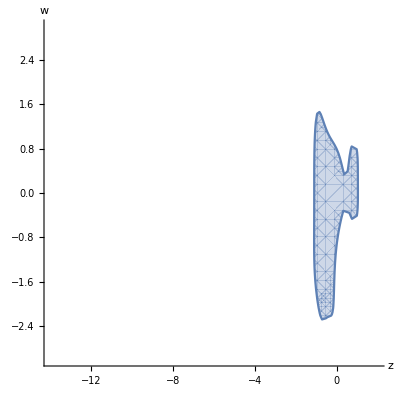

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.27622806801019867,4.586202890639971,-4.309973448641022,1.2299293752045668,-2.4347181364421893,1.7047881977185728,0.10655070833041062,-0.6389638953648463,1.3706649220569544,-1.2915849319369694,2.297275977168464,-0.005687848699002706,-0.0006546284196073803,4.426835784035641,-4.797568711084061,2.0939418168476536,-1.9042652754658125,0.9153533897264267,0.3264000229399668,0.31700572552656686,-0.785170879408249,1.0344401014901266,-1.0715630950688786,-1.127445298172489,0.11908781218934049,-0.9893204472617865,0.7232261921888061,1.1470062615057315,-2.1378790800639296,2.2882365383846444,0.34834344291878194,0.5012995986328709,-2.039430437882726,2.316796523212927,-0.113750293105376,-0.16361677963262253,3.1378767508479988,-2.2882340016755838,-0.34834219853695775,-0.5012999406632084,-1.331473079412136,2.3009952920518524,-2.6997616118429115,1.7302397112012218}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9060360.comet-31-08

{0.113592,-1.87262,2.18932,4.04538,-3.18606,-0.359327,0.415612,-0.111059,0.526662,0.939229,0.0676601,-0.00688879,0.0370441,-0.119006,1.67425,-0.185748,2.36463,-1.21132,-0.644738,1.97315,-0.780631,2.52129,-2.01897,-1.26622,-2.97345,3.50845,0.714864,-0.249859,0.00328217,-0.420406,0.414783,1.00234,0.908349,-1.82182,0.267426,0.646043,0.996722,0.420395,-0.414782,-1.00233,-3.31635,4.66406,1.01083,-2.35854}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

7.56742

-Graphics3D-

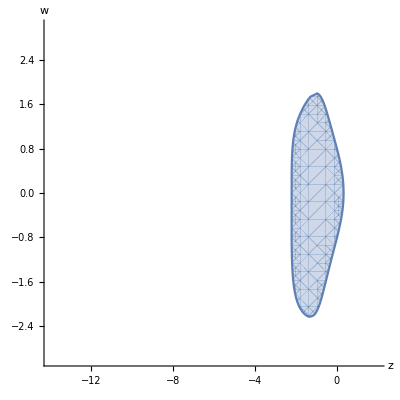

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.11359173574602198,-1.8726188497738716,2.1893226380027433,4.04538211129286,-3.186055511573977,-0.35932689260369494,0.415612342445249,-0.1110594188833126,0.5266624286881068,0.9392292987868001,0.06766006416678959,-0.006888786867557688,0.03704412962778706,-0.1190056489108845,1.674247915189363,-0.18574846644834642,2.3646304565137934,-1.2113176380742405,-0.6447383851480322,1.9731472737350755,-0.7806311731466471,2.521293594078323,-2.018965139893835,-1.2662216904498353,-2.9734546821348347,3.508449547918439,0.7148642802409588,-0.2498593408958851,0.0032821678697222342,-0.42040581843831204,0.4147825068315771,1.0023402207949332,0.9083489129514718,-1.8218177418086905,0.2674260263302545,0.6460425809201351,0.9967222637388331,0.42039505802361254,-0.4147819128631324,-1.002333805126359,-3.316346279539399,4.6640557111600724,1.0108268791449389,-2.3585368289788735}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

#### jOpt.9060354.comet-31-03

{0.459851,-0.587472,1.08745,1.67402,3.38612,-4.56014,0.0769662,0.612877,-0.535879,-0.75983,1.87521,-0.115385,0.0954955,-2.83863,4.36426,-3.75363,2.01017,2.73616,0.277413,-1.55956,2.84653,0.694645,-2.05218,0.405775,-0.0343296,0.427199,0.668949,-0.0618188,-2.37822,2.52873,0.0478029,0.801692,-2.66741,2.90307,-0.0132452,-0.22242,3.37824,-2.52874,-0.0478007,-0.801694,3.4104,-4.97805,1.28332,0.284328}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

8.08372

-Graphics3D-

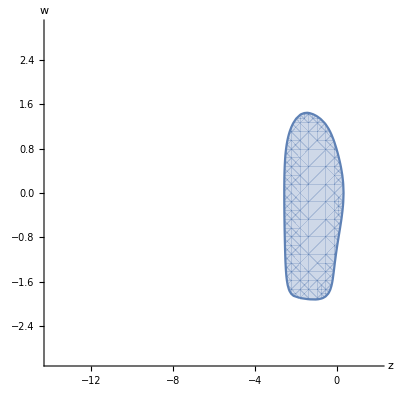

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.4598507989145295,-0.5874722529095457,1.0874523009877761,1.6740180369113327,3.3861187915865316,-4.560136584915967,0.0769661713372989,0.6128766267877671,-0.5358790742594493,-0.7598303239819446,1.8752149209608755,-0.1153851161004008,0.095495472856663,-2.838627009249854,4.364263645801639,-3.7536335754710146,2.010172956663475,2.73616488649968,0.27741301922174927,-1.559563068738087,2.8465318409940132,0.6946445040926884,-2.0521848916994876,0.4057749219004618,-0.034329573865120304,0.42719887479789503,0.6689490354792932,-0.06181875495185937,-2.3782237543713403,2.52872848506248,0.04780289782510631,0.8016919726660879,-2.667407130445926,2.903074391328017,-0.013245157023787995,-0.222420053092094,3.378237864446732,-2.5287437978681746,-0.047800739378405836,-0.8016936747934388,3.410402382890044,-4.978045917474247,1.2833157805436533,0.2843277273430467}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```